```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/home/zack/Desktop/snakingoscillators

#### Single trajectory runs

```mathematica
filebase="data/chimeras/3";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
Grid[{{rasterizeBackground[ListDensityPlot[theta[[1;;1000]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;1000]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[orders,ImageSize->300]]}}]

phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(#-#[[1]]&/@phases);
norms=Norm[#-dphases[[-1]]]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
If[Length[periods]>0,
period=Round[Mean[periods]];
Grid[{{rasterizeBackground[ListDensityPlot[theta[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[Length[periods]>0,{period,Mean[orders[[-period;;-1]]],Norm[Differences[dphases[[-period+1;;-1]]],2]}]
```

BinaryReadList::noopen: Cannot open data/chimeras/3phases.npy.

Part::take: Cannot take positions 17 through -1 in $Failed.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

BinaryReadList::noopen: Cannot open data/chimeras/3order.npy.

Part::take: Cannot take positions 17 through -1 in $Failed.

Part::take: Cannot take positions 1 through 1000 in ArcTan[Part[],Part[]].

ListDensityPlot::arrayerr: ArcTan[Part[],Part[]]⟦1;;1000⟧ must be a valid array.

Show::gtype: ListDensityPlot is not a type of graphics.

Options::optnf: Epilog is not a known option for ListDensityPlot[ArcTan[Part[],Part[]]⟦1;;1000⟧,AspectRatio→1,InterpolationOrder→0,ImageSize→300,PlotRange→All,ColorFunction→(Piecewise[{{Blend[{«2»},Times[«2»]], Slot[«1»]≤Times[«2»]}, {Blend[{«2»},Times[«2»]], Slot[«1»]≤0}, {Blend[{«2»},Times[«2»]], Slot[«1»]≤Times[«2»]}, {Blend[{«2»},Times[«2»]], Slot[«1»]≤π}}]&),ColorFunctionScaling→False].

Part::take: Cannot take positions 1 through 1000 in ArcTan[Part[],Part[]].

ListDensityPlot::arrayerr: ArcTan[Part[],Part[]]⟦1;;1000⟧ must be a valid array.

Show::gtype: ListDensityPlot is not a type of graphics.

Options::optnf: Epilog is not a known option for ListDensityPlot[ArcTan[Part[],Part[]]⟦1;;1000⟧,AspectRatio→1,InterpolationOrder→0,ImageSize→300,PlotRange→All,ColorFunction→(Piecewise[{{Blend[{«2»},Times[«2»]], Slot[«1»]≤Times[«2»]}, {Blend[{«2»},Times[«2»]], Slot[«1»]≤0}, {Blend[{«2»},Times[«2»]], Slot[«1»]≤Times[«2»]}, {Blend[{«2»},Times[«2»]], Slot[«1»]≤π}}]&),ColorFunctionScaling→False].

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: $Failed⟦17;;-1⟧ is not a list of numbers or pairs of numbers.

Show::gtype: ListPlot is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

Options::optnf: PlotRange is not a known option for ListPlot[$Failed⟦17;;-1⟧,ImageSize→300].

General::stop: Further output of Options::optnf will be suppressed during this calculation.

-Graphics- | -Graphics- | -Graphics-

Catenate::invrp: The argument Transpose[ArcTan[Part[],Part[]]] is not a valid Association or a list.

#### Chimeras from random initial conditions

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]/100}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
{bins,array}=HistogramList[vals[[All,2;;4]],{0.1}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
{#[[1]],#[[2]],#[[3]]*300,#[[4]]*100}&/@uniq

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Length[seeds]
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
```

33

{{130,5.56697×10^-17,0,0},{93,0.151249,148.392,61.289},{217,0.265035,148.392,70.6404},{444,0.269731,148.627,99.8012},{401,0.355893,469.261,145.457},{387,0.492707,148.392,50.0722},{28,0.431177,148.645,78.9475},{382,0.431175,148.645,93.884},{86,0.46834,296.963,93.7601},{247,0.462647,296.813,106.071},{180,0.417365,296.956,116.754},{143,0.467339,301.691,106.192},{18,0.416211,822.845,175.689},{67,0.516804,148.647,70.6027},{214,0.516825,148.647,93.4792},{296,0.593554,150.326,61.09},{36,0.548151,281.235,35.6414},{353,0.548149,281.235,60.8989},{7,0.534698,296.813,79.1075},{340,0.507703,296.994,93.1762},{271,0.533197,301.156,61.4421},{213,0.506523,301.669,79.0525},{245,0.50652,301.669,93.0974},{169,0.533197,564.675,84.9731},{427,0.687488,148.697,49.786},{290,0.687484,148.697,50.021},{73,0.602208,148.65,61.1531},{22,0.687482,148.697,70.5935},{154,0.680314,150.326,49.8897},{407,0.680316,150.326,50.0973},{317,0.773606,150.326,35.248},{383,0.773609,150.326,61.1116},{370,0.867984,0,0}}

33

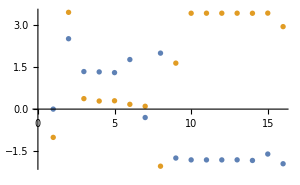
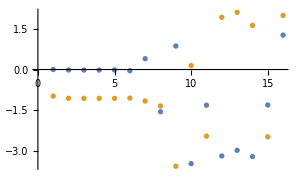
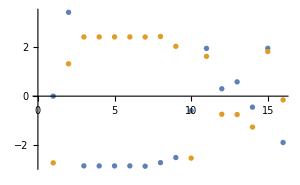
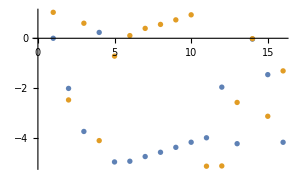
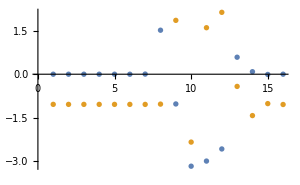
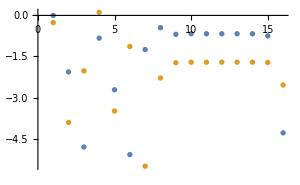
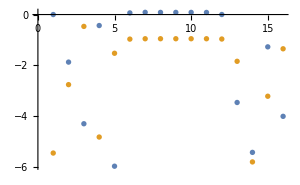
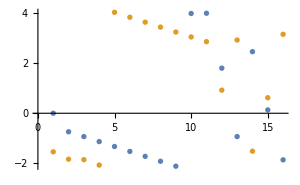
2 | 0.15124 | 148.391 | 61.2876 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.265045 | 148.391 | 70.6428 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.26974 | 148.628 | 99.8013 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 0.355903 | 905.08 | 150.422 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.4927 | 148.391 | 50.0741 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.431168 | 148.647 | 78.1863 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 0.431169 | 148.647 | 93.1436 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 0.468339 | 296.96 | 93.7553 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 0.462647 | 296.813 | 106.078 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
11 | 0.417373 | 296.953 | 116.268 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
12 | 0.467332 | 301.7 | 106.125 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
13 | 0.416211 | 435.789 | 128.214 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
14 | 0.516796 | 200.343 | 81.3357 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
15 | 0.516823 | 148.647 | 93.5828 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
16 | 0.593559 | 150.328 | 61.0902 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
17 | 0.548153 | 281.237 | 35.6422 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
18 | 0.548178 | 187.492 | 49.7293 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
19 | 0.534698 | 296.813 | 78.3898 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
20 | 0.507712 | 296.993 | 93.1788 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
21 | 0.533192 | 301.153 | 61.444 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
22 | 0.506509 | 301.667 | 79.0565 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
23 | 0.506513 | 301.667 | 93.0617 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
24 | 0.533192 | 301.153 | 61.6683 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
25 | 0.687487 | 148.697 | 50.3473 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
26 | 0.687484 | 148.697 | 50.0257 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
27 | 0.60222 | 148.65 | 61.1533 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
28 | 0.687482 | 148.697 | 70.5905 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
29 | 0.680312 | 150.328 | 49.8886 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
30 | 0.680312 | 150.328 | 50.0959 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
31 | 0.773606 | 150.328 | 35.248 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
32 | 0.773609 | 150.328 | 61.1123 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(#-#[[1]]&/@phases);
If[period>0,
{Grid[{{j,order,period,norm,rasterizeBackground[ListDensityPlot[theta[[1;;Round[period/0.1];;10]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;Round[period/0.1];;10]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

#### Plot auto results

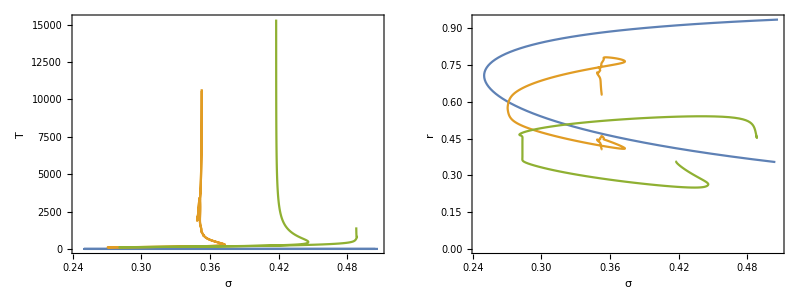

```mathematica
Grid[{{ListPlot[{Import["auto/rel/janus_rels.dat"][[1;;-2,{1,7}]],Import["auto/rel/janus_rel1.dat"][[1;;-2,{1,7}]],Import["auto/rel/janus_rel2.dat"][[1;;-2,{1,7}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1],ListPlot[{Import["auto/rel/janus_rels.dat"][[1;;-2,{1,8}]],Import["auto/rel/janus_rel1.dat"][[1;;-2,{1,8}]],Import["auto/rel/janus_rel2.dat"][[1;;-2,{1,8}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1]}}]
```